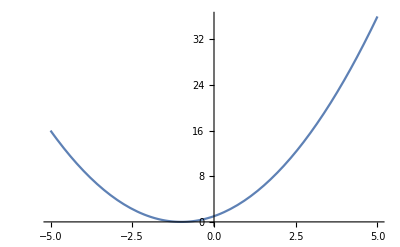

```mathematica
Plot[(x+1)^2,{x,-5,5}]
```

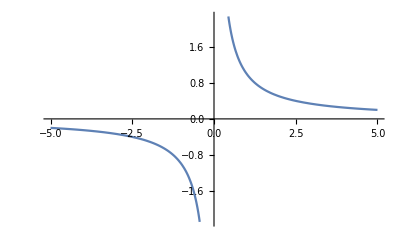

```mathematica
Plot[1/x,{x,-5,5}]
```

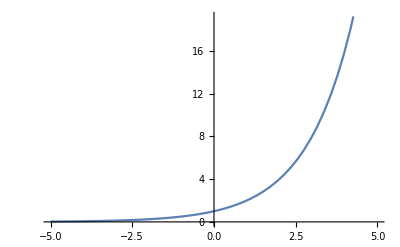

```mathematica
Plot[2^x,{x,-5,5}]
```

## Exercise 2 - Polynomials

```mathematica
f[x_]:=2 x^6+6 x^5+x^3-7 x^2+3x+14
```

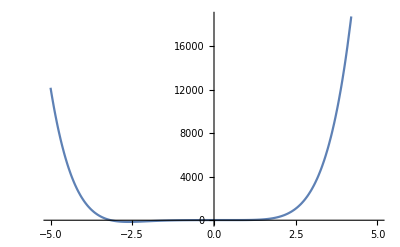

```mathematica
Plot[f[x],{x,-5,5}]
```

```mathematica
f[45]
```

17714777099

## Exercise 3 - Rational

```mathematica
f[x_]:=(x^3+6x-7)/(20 x^4+4 x^3-359 x^2-130 x+888)
```

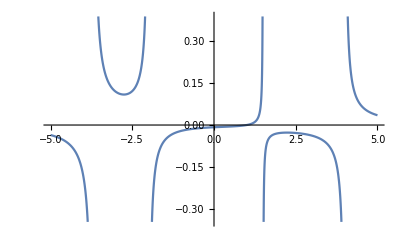

```mathematica
Plot[f[x],{x,-5,5}]
```

```mathematica
Solve[20 x^4+x^3-359 x^2+130x+888==0,x]
```

{{x→Root-4.14Root[888+130 #1-359 #1^2+#1^3+20 #1^4&,1]-4.139586273036064},{x→Root-1.48Root[888+130 #1-359 #1^2+#1^3+20 #1^4&,2]-1.4820866915301536},{x→Root2.06Root[888+130 #1-359 #1^2+#1^3+20 #1^4&,3]2.0619667720307953},{x→Root3.51Root[888+130 #1-359 #1^2+#1^3+20 #1^4&,4]3.5097061925354227}}

```mathematica
Solve[20 x^4+4 x^3-359 x^2-130 x+888==0,x]
```

{{x→-37/10},{x→-2},{x→3/2},{x→4}}

```mathematica
FunctionDomain[f[x],x]
```

x<-37/10||-37/10<x<-2||-2<x<3/2||3/2<x<4||x>4

## Exercise 4 - Planet Aurora

```mathematica
daylight[t_]:= 15+4.7Cos[2π/501(t-240)]
```

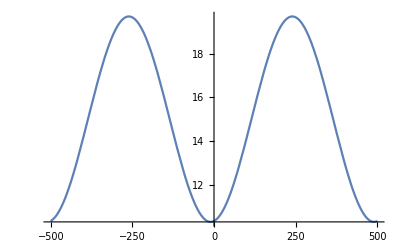

```mathematica
Plot[daylight[t],{t,-501,501}]
```

```mathematica
daylight[397]
```

13.1776

## Exercise 5 - Bacteria Colony

```mathematica
bacterialgrowth[t_]:=1.97^t
```

```mathematica
bacterialdecay[m_,t_]:=m*0.67^t
```

```mathematica
bacterialgrowth[30]
```

6.82318×10^8

```mathematica
Solve[1000==bacterialdecay[bacterialgrowth[30],t],t] //Quiet
```

{{t→33.5431}}

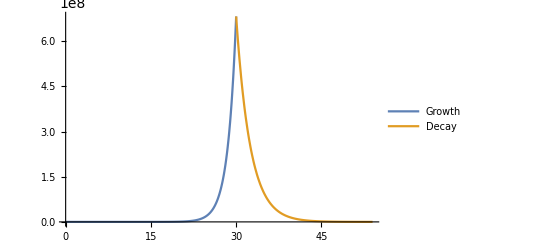

```mathematica
Plot[{Piecewise[{{bacterialgrowth[t], 0<=t<=30}, {Null, True}}] , Piecewise[{{bacterialdecay[bacterialgrowth[30],t-30], 30<=t<=54}, {Null, True}}]}, {t, 0, 54}, Sequence[
 PlotRange -> All, PlotLegends -> {"Growth", "Decay"}]]
```